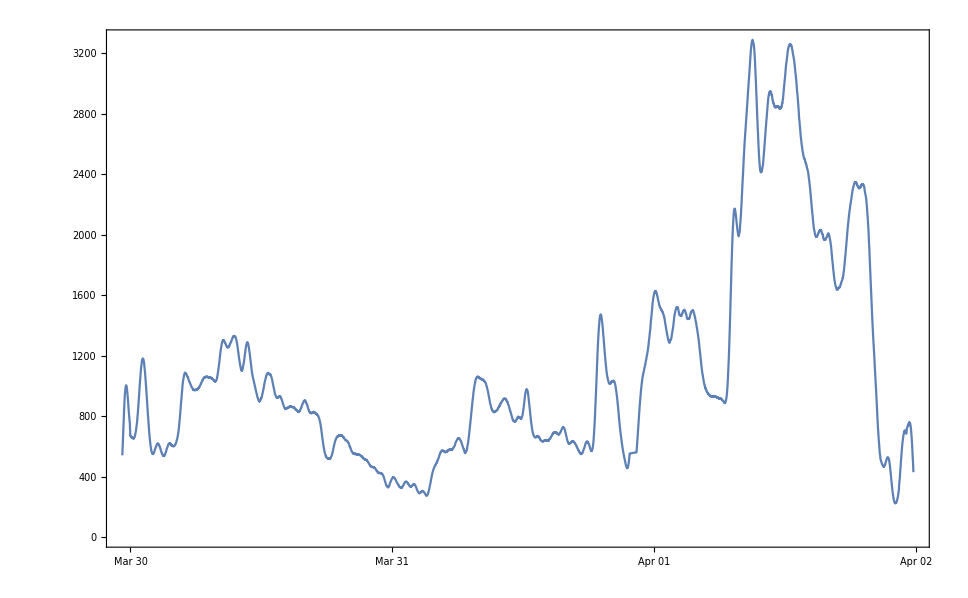

```mathematica
raw  = Import["/Users/hesicong/Desktop/AIR.CSV", "CSV"];
dates = raw[[;;,1]];
data = GaussianFilter[raw[[;;,2]],50];
d = {dates, data}ᵀ;
DateListPlot[d, Ticks->{dates,Automatic}]
```